```mathematica
SetDirectory["~/w2013/stat245/scripts_5/11_44"]
```

/home/hall/w2013/stat245/scripts_5/11_44

```mathematica
sz=Import["data_cd_sz","List"]
```

{16.6,0.19,33.3,0.44,34.1,0.39,0.,0.,119.8,1.75,0.1,0.01,25.3,0.27,359.3,5.99,6.6,0.1,0.4,0.01,62.8,0.68,0.2,0.01,13.,0.15,0.,0.,0.,0.,5.9,0.1,0.1,0.01,6.,0.07,32.1,0.42,0.,0.}

```mathematica
nsz=Import["data_cd_norm","List"]
```

{289.4,3.96,0.,0.,620.4,7.95,0.,0.,8.5,0.1,5.5,0.09,43.2,0.91,91.7,1.,200.9,3.46,113.8,2.01,102.2,1.5,108.2,1.98,36.9,0.49,122.,1.72,101.9,1.52}

```mathematica
szTot=Take[sz,{1,40,2}]
```

{16.6,33.3,34.1,0.,119.8,0.1,25.3,359.3,6.6,0.4,62.8,0.2,13.,0.,0.,5.9,0.1,6.,32.1,0.}

```mathematica
szMg=Take[sz,{2,40,2}]
```

{0.19,0.44,0.39,0.,1.75,0.01,0.27,5.99,0.1,0.01,0.68,0.01,0.15,0.,0.,0.1,0.01,0.07,0.42,0.}

```mathematica
nTot=Take[nsz,{1,30,2}]
```

{289.4,0.,620.4,0.,8.5,5.5,43.2,91.7,200.9,113.8,102.2,108.2,36.9,122.,101.9}

```mathematica
nMg=Take[nsz,{2,30,2}]
```

{3.96,0.,7.95,0.,0.1,0.09,0.91,1.,3.46,2.01,1.5,1.98,0.49,1.72,1.52}

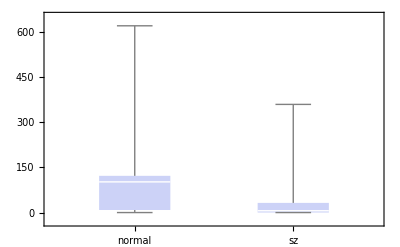

```mathematica
BoxWhiskerChart[{nTot,szTot},ChartLabels->{"normal","sz"}]
```

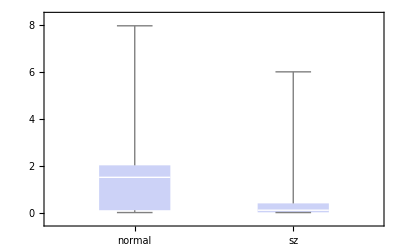

```mathematica
BoxWhiskerChart[{nMg,szMg},ChartLabels->{"normal","sz"}]
```

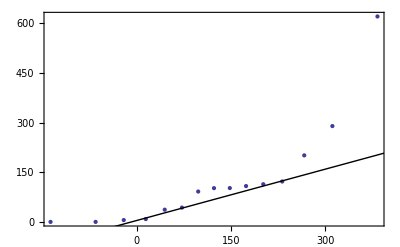

```mathematica
QuantilePlot[nTot]
```

```mathematica
makeTStat[x_,y_]:=(Mean[x]-Mean[y])/Sqrt[Variance[x]/Length[x]+Variance[y]/Length[y]]
```

```mathematica
makeDof[x_,y_]:=(Variance[x]/Length[x]+Variance[y]/Length[y])^2/((Variance[x]/Length[x])^2/(Length[x]-1)+(Variance[y]/Length[y])^2/(Length[y]-1))
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
Variance[nTot]
```

25305.9

```mathematica
Variance[szTot]
```

6646.82

```mathematica
Variance[nMg]
```

4.35221

```mathematica
Variance[szMg]
```

1.81455

```mathematica
makeTStat[nTot,szTot]
```

1.94032

```mathematica
makeDof[nTot,szTot]
```

19.5015

```mathematica
StudentTPValue[2.025,23,TwoSided->True]
```

TwoSidedPValue→0.0546269

```mathematica
makeTStat[nMg,szMg]
```

2.02517

```mathematica
makeDof[nMg,szMg]
```

22.5031